```mathematica
Find rule type;
type[L_,x_]:=
If[Intersection[L[[L[[x]][[1]]]],{L[[x]][[2]]}]=={}&&
Intersection[L[[L[[x]][[2]]]],{L[[x]][[3]]}]=={}&&
Intersection[L[[L[[x]][[3]]]],{L[[x]][[1]]}]=={},1,
If[Intersection[L[[L[[x]][[1]]]],{L[[x]][[2]]}]=={}&&
Intersection[L[[L[[x]][[1]]]],{L[[x]][[3]]}]=={}&&
Intersection[L[[L[[x]][[2]]]],{L[[x]][[3]]}]!={},2,
If[Intersection[L[[L[[x]][[1]]]],{L[[x]][[2]]}]=={}&&
Intersection[L[[L[[x]][[2]]]],{L[[x]][[3]]}]=={}&&
Intersection[L[[L[[x]][[1]]]],{L[[x]][[3]]}]!={},3,
If[Intersection[L[[L[[x]][[1]]]],{L[[x]][[3]]}]=={}&&
Intersection[L[[L[[x]][[2]]]],{L[[x]][[3]]}]=={}&&
Intersection[L[[L[[x]][[1]]]],{L[[x]][[2]]}]!={},4,5]]]];

Apply rules;
unchangedold[L_,x_,c_]:=
{
L,
Join[{x},L[[x]],L[[L[[x]][[1]]]],L[[L[[x]][[2]]]],L[[L[[x]][[3]]]]],
c};


unchanged[L_,x_,c_]:=Module[{dummy},AppendTo[cnet,{x,{L[[x]],{L[[L[[x]][[1]]]],L[[L[[x]][[2]]]],L[[L[[x]][[3]]]]}}}];
{
L,
Join[{x},L[[x]],L[[L[[x]][[1]]]],L[[L[[x]][[2]]]],L[[L[[x]][[3]]]]],
c}];

tri[L_,x_,c_]:=Module[{l=Length[L],a1=L[[x]][[1]],a2=L[[x]][[2]],a3=L[[x]][[3]]},AppendTo[cnet,{x,{L[[x]],{a1,l+1,l+2}},{L[[a2]],ReplacePart[L[[a2]],2->l+2]},{L[[a3]],ReplacePart[L[[a3]],3->l+1]}}];
{
Join[ReplacePart[L,{x->{a1,l+1,l+2},a2->ReplacePart[L[[a2]],2->l+2],a3->ReplacePart[L[[a3]],3->l+1]}],{{l+2,x,a3},{l+1,a2,x}}],

{x,l+1,l+2,a1,a2,a3,L[[a1]][[2]],L[[a1]][[3]],L[[a2]][[1]],L[[a2]][[3]],L[[a3]][[1]],L[[a3]][[2]]},

If[c=={},{},
Join[ReplacePart[c,x->(0.5*c[[x]]+0.5*c[[a1]])],{(0.5*c[[x]]+0.5*c[[a3]]),(0.5*c[[x]]+0.5*c[[a2]])}]]
}
];


cross[x1_,x2_,y1_,y2_]:=FindInstance[x1*a+(1-a)*x2==y1*b+(1-b)*y2&&0≤a≤1&&0≤b≤1,{a,b}];

swingred[L_,x_,y_,c_]:=Module[{x2=L[[x]][[2]],x3=L[[x]][[3]],y2=L[[y]][[2]],y3=L[[y]][[3]]},AppendTo[cnet,{x,{L[[x]],{y,x2,y3}},{L[[y]],{x,y2,x3}},{L[[y3]],ReplacePart[L[[y3]],3->x]},{L[[x3]],ReplacePart[L[[x3]],3->y]}}];
{
ReplacePart[L,{x->{y,x2,y3},y->{x,y2,x3},y3->ReplacePart[L[[y3]],3->x],x3->ReplacePart[L[[x3]],3->y]}],

Join[{x,y,x2,x3,y2,y3},L[[x2]],L[[x3]]],

If[c=={},{},
If[cross[c[[x2]],c[[y3]],c[[y2]],c[[x3]]]=={},
ReplacePart[c,{x->0.5*(c[[x2]]+c[[y3]]),y->0.5*(c[[x3]]+c[[y2]])}],
ReplacePart[c,{x->0.5*(c[[x2]]+c[[y2]]),y->0.5*(c[[x3]]+c[[y3]])}]
]
]
}
];

swingblue[L_,x_,y_,c_]:=Module[{x1=L[[x]][[1]],x3=L[[x]][[3]],y1=L[[y]][[1]],y3=L[[y]][[3]]},AppendTo[cnet,{x,{L[[x]],{x1,y,y3}},{L[[y]],{y1,x,x3}},{L[[y3]],ReplacePart[L[[y3]],3->x]},{L[[x3]],ReplacePart[L[[x3]],3->y]}}];
{
ReplacePart[L,{x->{x1,y,y3},y->{y1,x,x3},y3->ReplacePart[L[[y3]],3->x],x3->ReplacePart[L[[x3]],3->y]}],

Join[{x,y,x1,x3,y1,y3},L[[x1]],L[[x3]]],

If[c=={},{},
If[cross[c[[x1]],c[[y3]],c[[y1]],c[[x3]]]=={},
ReplacePart[c,{x->0.5*(c[[x1]]+c[[y3]]),y->0.5*(c[[x3]]+c[[y1]])}],
ReplacePart[c,{x->0.5*(c[[x1]]+c[[y1]]),y->0.5*(c[[x3]]+c[[y3]])}]
]
]
}
];

swinggreen[L_,x_,y_,c_]:=Module[{x1=L[[x]][[1]],x2=L[[x]][[2]],y1=L[[y]][[1]],y2=L[[y]][[2]]},AppendTo[cnet,{x,{L[[x]],{y1,x2,y}},{L[[y]],{x1,y2,x}},{L[[y1]],ReplacePart[L[[y1]],1->x]},{L[[x1]],ReplacePart[L[[x1]],1->y]}}];
{
ReplacePart[L,{x->{y1,x2,y},y->{x1,y2,x},y1->ReplacePart[L[[y1]],1->x],x1->ReplacePart[L[[x1]],1->y]}],

Join[{x,y,x1,x2,y1,y2},L[[x1]],L[[x2]]],

If[c=={},{},
If[cross[c[[x2]],c[[y1]],c[[x1]],c[[y2]]]=={},
ReplacePart[c,{x->0.5*(c[[x2]]+c[[y1]]),y->0.5*(c[[x1]]+c[[y2]])}],
ReplacePart[c,{x->0.5*(c[[x2]]+c[[y2]]),y->0.5*(c[[x1]]+c[[y1]])}]
]
]
}
];

fall[a_,b_,x_]:=If[x<Min[a,b],x,If[x>Max[a,b],x-2,x-1]];


untrired[L_,x_,c_]:=Module[{a1=L[[x]][[1]],a2=L[[x]][[2]],a3=L[[x]][[3]]},Module[{a12=L[[a1]][[2]],a13=L[[a1]][[3]],a21=L[[a2]][[1]],a23=L[[a2]][[3]],a31=L[[a3]][[1]],a32=L[[a3]][[2]]},AppendTo[cnet,{x,{L[[a23]],ReplacePart[L[[a23]],3->x]},{L[[a32]],ReplacePart[L[[a32]],2->x]}}];
If[a32==a23,{},
{
Map[Map[fall[a2,a3,#]&,#]&,Delete[ReplacePart[L,{x->{a1,a32,a23},a23->ReplacePart[L[[a23]],3->x],a32->ReplacePart[L[[a32]],2->x]}],{{a2},{a3}}]],

Map[fall[a2,a3,#]&,{x,a1,a32,a23,a12,a13}],

If[c=={},{},
Delete[c,{{a2},{a3}}]]
}
]
]];

untriblue[L_,x_,c_]:=Module[{a1=L[[x]][[1]],a2=L[[x]][[2]],a3=L[[x]][[3]]},Module[{a12=L[[a1]][[2]],a13=L[[a1]][[3]],a21=L[[a2]][[1]],a23=L[[a2]][[3]],a31=L[[a3]][[1]],a32=L[[a3]][[2]]},AppendTo[cnet,{x,{L[[x]],{a31,a2,a13}},{L[[a13]],ReplacePart[L[[a13]],3->x]},{L[[a31]],ReplacePart[L[[a31]],1->x]}}];
If[a31==a13,{},
{
Map[Map[fall[a1,a3,#]&,#]&,Delete[ReplacePart[L,{x->{a31,a2,a13},a13->ReplacePart[L[[a13]],3->x],a31->ReplacePart[L[[a31]],1->x]}],{{a1},{a3}}]],

Map[fall[a1,a3,#]&,{x,a2,a13,a31,a21,a23}],

If[c=={},{},
Delete[c,{{a1},{a3}}]]
}
]
]];

untrigreen[L_,x_,c_]:=Module[{a1=L[[x]][[1]],a2=L[[x]][[2]],a3=L[[x]][[3]]},Module[{a12=L[[a1]][[2]],a13=L[[a1]][[3]],a21=L[[a2]][[1]],a23=L[[a2]][[3]],a31=L[[a3]][[1]],a32=L[[a3]][[2]]},AppendTo[cnet,{x,{L[[x]],{a21,a12,a3}},{L[[a21]],ReplacePart[L[[a21]],1->x]},{L[[a12]],ReplacePart[L[[a12]],2->x]}}];
If[a21==a12,{},
{
Map[Map[fall[a1,a2,#]&,#]&,Delete[ReplacePart[L,{x->{a21,a12,a3},a21->ReplacePart[L[[a21]],1->x],a12->ReplacePart[L[[a12]],2->x]}],{{a1},{a2}}]],

Map[fall[a1,a2,#]&,{x,a3,a12,a21,a31,a32}],

If[c=={},{},
Delete[c,{{a1},{a2}}]]
}
]
]];

Execute writer;
applyn[L_,x_,t_,r_,c_]:=
If[t==1,
If[r≤13,
Module[{KK=unchanged[L,x,c]},
ReplacePart[KK,2->KK[[2]][[r]]]],
If[r≤ 25,
Module[{KK=tri[L,x,c]},
ReplacePart[KK,2->KK[[2]][[r-13]]]],
If[r≤37,
Module[{KK=swingred[L,x,L[[x]][[1]],c]},
ReplacePart[KK,2->KK[[2]][[r-25]]]],
If[r≤49,
Module[{KK=swingblue[L,x,L[[x]][[2]],c]},
ReplacePart[KK,2->KK[[2]][[r-37]]]],
Module[{KK=swinggreen[L,x,L[[x]][[3]],c]},
ReplacePart[KK,2->KK[[2]][[r-49]]]]
]]]],
If[t≤4,
If[r≤13,
Module[{KK=unchanged[L,x,c]},triA[L,x,c];
ReplacePart[KK,2->KK[[2]][[r]]]],
If[r≤25,
Module[{KK=tri[L,x,c]},
ReplacePart[KK,2->KK[[2]][[r-13]]]],
If[r≤37,
If[t==2,
Module[{KK=swingred[L,x,L[[x]][[1]],c]},
ReplacePart[KK,2->KK[[2]][[r-25]]]],
If[t==3,
Module[{KK=swingblue[L,x,L[[x]][[2]],c]},
ReplacePart[KK,2->KK[[2]][[r-25]]]],
Module[{KK=swinggreen[L,x,L[[x]][[3]],c]},
ReplacePart[KK,2->KK[[2]][[r-25]]]]
]],

If[t==2,
Module[{KK=untrired[L,x,c]},
ReplacePart[KK,2->KK[[2]][[r-37]]]],
If[t==3,
Module[{KK=untriblue[L,x,c]},
ReplacePart[KK,2->KK[[2]][[r-37]]]],
Module[{KK=untrigreen[L,x,c]},
ReplacePart[KK,2->KK[[2]][[r-37]]]]
]]],
{L,x,c}
]]]];

u[X_,R_]:=Module[{t=type[X[[1]],X[[2]]]},
If[t>4,X,
applyn[X[[1]],X[[2]],t,R[[t]],X[[3]]]]];

ListToMat[L_]:=Table[ReplacePart[ConstantArray[0,Length[L]],Map[#->1&,L[[i]]]],{i,1,Length[L]}];

ListToMatCol[L_]:=Table[
ReplacePart[ReplacePart[ReplacePart[ConstantArray[0,Length[L]],L[[i]][[1]]->1],L[[i]][[2]]->2],L[[i]][[3]]->3],
{i,Length[L]}];

randomrule[]:={RandomInteger[{14,25}],RandomInteger[{1,43}],RandomInteger[{1,43}],RandomInteger[{1,43}]};
ZZ=Table[randomrule[],{i,1,5000}];
cnet={};
start={{{2,4,8},{1,3,7},{4,2,6},{3,1,5},{6,8,4},{5,7,3},{8,6,2},{7,5,1}},1,{}};

Create network and show;
showit1[r_,t_]:=
AdjacencyGraph[ListToMat[Nest[u[#,r]&,start,t][[1]]],ImageSize->1.2{500, 300}];
Create network and not show;

showit2[r_,t_]:=
Nest[u[#,r]&,start,t][[1]];

GetPriorEvents[list_,cpair2_]:=Module[{elist},elist=Select[cpair2[[list[[1]]]],#[[1]]==list[[1]]&&#[[2]]<list[[2]]&];If[Length[elist]>0,Last[elist],{}]]//.{}->Sequence[]

CreateCausalNetwork[list_]:=Module[{cpair, cpair2, cevents, events},cpair=SortBy[Union[Partition[Riffle[Union[Flatten[start[[1]]]],ConstantArray[0,8]],2],Flatten[Table[Partition[Riffle[Union[Flatten[#[[2]]&/@Take[cnet[[e]],{2,Length[cnet[[e]]]}]]],ConstantArray[e,Length[Union[Flatten[#[[2]]&/@Take[cnet[[e]],{2,Length[cnet[[e]]]}]]]]]],2],{e,Length[cnet]}],1]],First];
cpair2=GatherBy[cpair,First];
cevents=Partition[Riffle[#[[1]],ConstantArray[#[[2]],Length[#[[1]]]]],2]&/@Table[{Union[Flatten[Take[cnet[[i]],{2,Length[cnet[[i]]]}][[All,2]]]],i},{i,Length[cnet]}]//.{}->Sequence[];
events=Table[Table[GetPriorEvents[cevents[[i]][[k]],cpair2],{k,Length[cevents[[i]]]}],{i,1,Length[cevents]}];
g=Graph[Rule@@@Flatten[Partition[Riffle[#[[1]],ConstantArray[#[[2]],Length[#[[1]]]]],2]&/@Table[{Union[events[[i]][[All,2]]],i},{i,Length[events]}],1],AspectRatio->Automatic,DirectedEdges->{True,"ArrowheadsSize"->0.0005}]
]
```

```mathematica
Function to calculate causal net from events stored in variable cnet;
GenerateCausalSets[rule_,t_]:=Module[{start={{{2,4,8},{1,3,7},{4,2,6},{3,1,5},{6,8,4},{5,7,3},{8,6,2},{7,5,1}},1,{}}},cnet={};
showit2[Module[{LLk=1+IntegerDigits[rule,43,4]},
If[LLk[[1]]<14,ReplacePart[LLk,1->14],If[LLk[[1]]>25,ReplacePart[LLk,1->25],LLk]]],t];
CreateCausalNetwork[cnet]]
```

```mathematica
Create causal net wirh rule number (up to 1645074)& number of time steps t;
```

#### Call function to generate adjecency matrices for causal sets. CreateCSSeriesTrinetReplacement[rule#, iterations]

```mathematica
CreateCSSeriesTrinetReplacement[rule_,n_]:=Table[GenerateCausalSets[rule,i],{i,1,n}]
```



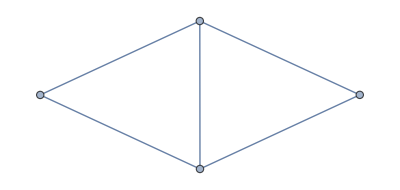
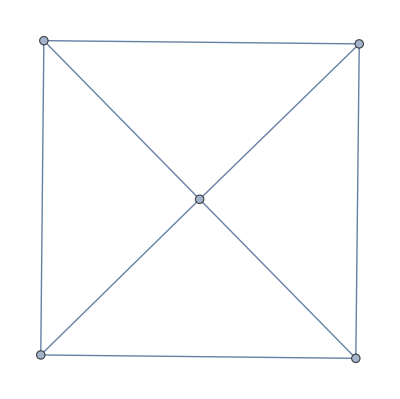
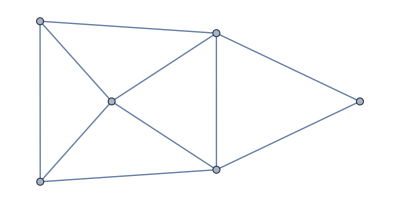
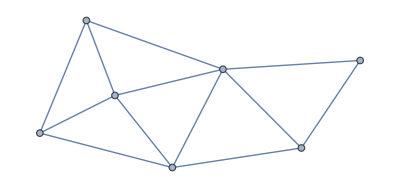
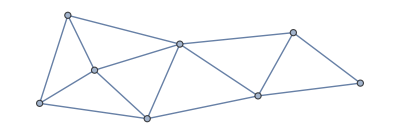
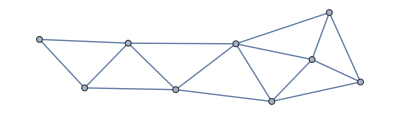
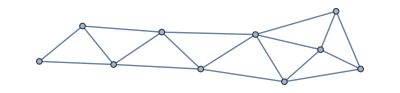
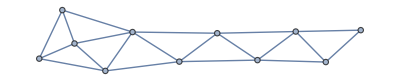

```mathematica
CreateCSSeriesTrinetReplacement[2345,10]
```